this is about some bump functions and their derivatives.

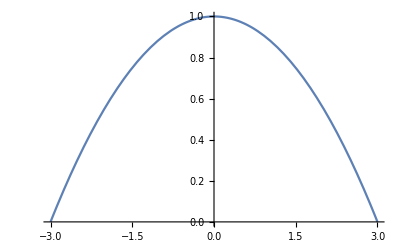

```mathematica
f[x_, a_, b_] := a(1-(x/b)^2)
Plot[f[x, 1, 3], {x, -3,3}]
```

```mathematica
Plot[f[x, 1, 3], {x, -3,3}]
```

-Graphics-

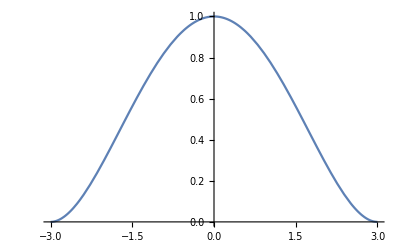

```mathematica
g[x_, a_, b_] := a/b^4 (x-b)^2(x+b)^2 
Plot[g[x, 1, 3], {x, -3, 3}]
```

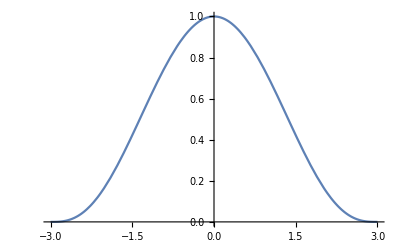

```mathematica
h[x_, a_, b_] := -a/b^6(x-b)^3(x+b)^3
Plot[h[x, 1, 3], {x, -3, 3}]
```

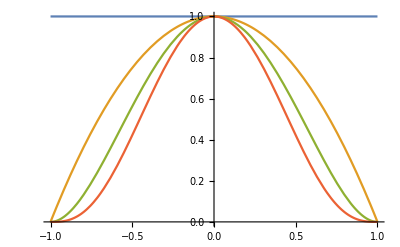

```mathematica
Plot[{1, f[x, 1, 1],g[x,1,1], h[x,1,1]}, {x, -1, 1}]
```

```mathematica
2/L ∫_-b^b Cos[n Pi x/L] f[x, a,b]ⅆx
```

(8 a L (-b n π Cos[(b n π)/L]+L Sin[(b n π)/L]))/(b^2 n^3 π^3)

```mathematica
1/L ∫_-b^b f[x, a,b]ⅆx
```

(4 a b)/(3 L)

```mathematica
2/Pi ∫_-b^b Cos[n x] f[x, a,b]ⅆx
```

(8 a (-b n Cos[b n]+Sin[b n]))/(b^2 n^3 π)

The coefficient does  not depend on L if the bump goes to beta L.

```mathematica
4/L ∫_0^(β L) Cos[n Pi x/L] f[x, a,β L]ⅆx
```

-(8 a (n π β Cos[n π β]-Sin[n π β]))/(n^3 π^3 β^2)

```mathematica
2/L ∫_0^(β L) f[x, a,β L]ⅆx
```

(4 a β)/3

Now do this for constant (standard) and g and h
First the constant:

```mathematica
2/L ∫_0^(β L) aⅆx
```

2 a β

```mathematica
4/L ∫_0^(β L) Cos[n Pi x/L] aⅆx
```

(4 a Sin[n π β])/(n π)

Now g (which is Continuous but not C1)

```mathematica
Simplify[1/L ∫_(-β L)^(β L) g[x, a,β L]ⅆx]
```

(16 a β)/15

```mathematica
Simplify[4/L ∫_0^(β L) Cos[n Pi x/L] g[x, a,β L]ⅆx]
```

-(32 a (3 n π β Cos[n π β]+(-3+n^2 π^2 β^2) Sin[n π β]))/(n^5 π^5 β^4)

```mathematica
Simplify[4/L ∫_0^(β L) Cos[n Pi x/L] h[x, a,β L]ⅆx]
```

(192 a (n π β (-15+n^2 π^2 β^2) Cos[n π β]+3 (5-2 n^2 π^2 β^2) Sin[n π β]))/(n^7 π^7 β^6)

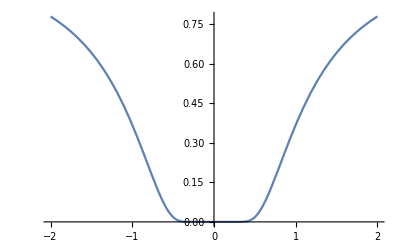

```mathematica
Plot[Exp[-1/x^2], {x, -2,2}]
```

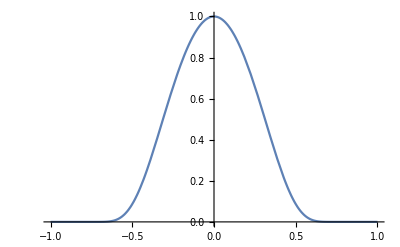

```mathematica
Plot[E^2 Exp[-1/(x-1)^2] Exp[-1/(x+1)^2], {x, -1,1}]
```

```mathematica
Simplify[2 - 1/(x-1)^2 -1/(x+1)^2]
```

(2 x^2 (-3+x^2))/((-1+x^2)^2)

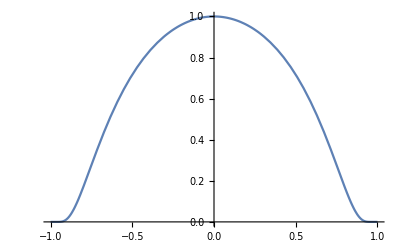

```mathematica
Plot[Exp[x^2/(x^2-1)], {x, -1,1}]
```

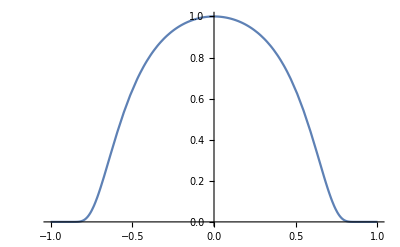

```mathematica
Plot[Exp[-x^2/(x^2-1)^2], {x, -1,1}]
```